## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.1; Q=0.99;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.171733-8.26537×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.0867609

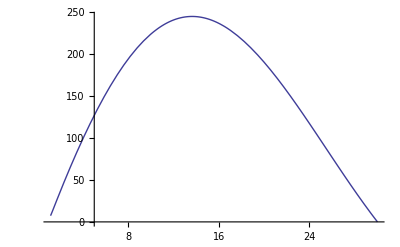

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}]
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,0.171733},{30.2,0.171043},{30.4,0.170363},{30.6,0.169692},{30.8,0.16903},{31.,0.168377},{31.2,0.167734},{31.4,0.167099},{31.6,0.166473},{31.8,0.165855},{32.,0.165245},{32.2,0.164644},{32.4,0.164051},{32.6,0.163466},{32.8,0.162888},{33.,0.162318},{33.2,0.161756},{33.4,0.161201},{33.6,0.160653},{33.8,0.160112},{34.,0.159578},{34.2,0.159051},{34.4,0.158531},{34.6,0.158018},{34.8,0.157511},{35.,0.15701},{35.2,0.156516},{35.4,0.156028},{35.6,0.155546},{35.8,0.15507},{36.,0.1546},{36.2,0.154136},{36.4,0.153677},{36.6,0.153224},{36.8,0.152777},{37.,0.152335},{37.2,0.151899},{37.4,0.151467},{37.6,0.151041},{37.8,0.15062},{38.,0.150204},{38.2,0.149793},{38.4,0.149387},{38.6,0.148986},{38.8,0.148589},{39.,0.148198},{39.2,0.14781},{39.4,0.147427},{39.6,0.147049},{39.8,0.146675},{40.,0.146305},{40.2,0.14594},{40.4,0.145578},{40.6,0.145221},{40.8,0.144868},{41.,0.144519},{41.2,0.144174},{41.4,0.143833},{41.6,0.143495},{41.8,0.143161},{42.,0.142831},{42.2,0.142505},{42.4,0.142182},{42.6,0.141863},{42.8,0.141547},{43.,0.141235},{43.2,0.140926},{43.4,0.140621},{43.6,0.140318},{43.8,0.14002},{44.,0.139724},{44.2,0.139431},{44.4,0.139142},{44.6,0.138855},{44.8,0.138572},{45.,0.138292},{45.2,0.138014},{45.4,0.13774},{45.6,0.137468},{45.8,0.1372},{46.,0.136934},{46.2,0.136671},{46.4,0.13641},{46.6,0.136152},{46.8,0.135897},{47.,0.135645},{47.2,0.135395},{47.4,0.135147},{47.6,0.134902},{47.8,0.13466},{48.,0.13442},{48.2,0.134182},{48.4,0.133947},{48.6,0.133714},{48.8,0.133484},{49.,0.133256},{49.2,0.13303},{49.4,0.132806},{49.6,0.132584},{49.8,0.132365},{50.,0.132148},{50.2,0.131933},{50.4,0.13172},{50.6,0.131509},{50.8,0.1313},{51.,0.131093},{51.2,0.130888},{51.4,0.130685},{51.6,0.130484},{51.8,0.130285},{52.,0.130088},{52.2,0.129892},{52.4,0.129699},{52.6,0.129507},{52.8,0.129317},{53.,0.129129},{53.2,0.128943},{53.4,0.128758},{53.6,0.128575},{53.8,0.128394},{54.,0.128215},{54.2,0.128037},{54.4,0.12786},{54.6,0.127686},{54.8,0.127513},{55.,0.127341},{55.2,0.127171},{55.4,0.127003},{55.6,0.126836},{55.8,0.126671},{56.,0.126507},{56.2,0.126344},{56.4,0.126183},{56.6,0.126024},{56.8,0.125866},{57.,0.125709},{57.2,0.125554},{57.4,0.1254},{57.6,0.125247},{57.8,0.125096},{58.,0.124946},{58.2,0.124797},{58.4,0.12465},{58.6,0.124504},{58.8,0.124359},{59.,0.124215},{59.2,0.124073},{59.4,0.123932},{59.6,0.123792},{59.8,0.123653},{60.,0.123516},{60.2,0.123379},{60.4,0.123244},{60.6,0.12311},{60.8,0.122977},{61.,0.122845},{61.2,0.122714},{61.4,0.122585},{61.6,0.122456},{61.8,0.122329},{62.,0.122202},{62.2,0.122077},{62.4,0.121952},{62.6,0.121829},{62.8,0.121707},{63.,0.121585},{63.2,0.121465},{63.4,0.121346},{63.6,0.121227},{63.8,0.12111},{64.,0.120993},{64.2,0.120878},{64.4,0.120763},{64.6,0.120649},{64.8,0.120537},{65.,0.120425},{65.2,0.120314},{65.4,0.120204},{65.6,0.120094},{65.8,0.119986},{66.,0.119878},{66.2,0.119772},{66.4,0.119666},{66.6,0.119561},{66.8,0.119457},{67.,0.119353},{67.2,0.119251},{67.4,0.119149},{67.6,0.119048},{67.8,0.118948},{68.,0.118848},{68.2,0.11875},{68.4,0.118652},{68.6,0.118554},{68.8,0.118458},{69.,0.118362},{69.2,0.118267},{69.4,0.118173},{69.6,0.118079},{69.8,0.117987},{70.,0.117894}}

```mathematica
winit=(0.10+0.000005*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=190+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,200}]
t2r2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{190.,0.102698},{190.2,0.102692},{190.4,0.102687},{190.6,0.102681},{190.8,0.102675},{191.,0.10267},{191.2,0.102665},{191.4,0.102659},{191.6,0.102654},{191.8,0.102648},{192.,0.102643},{192.2,0.102637},{192.4,0.102632},{192.6,0.102627},{192.8,0.102621},{193.,0.102616},{193.2,0.102611},{193.4,0.102605},{193.6,0.1026},{193.8,0.102595},{194.,0.10259},{194.2,0.102585},{194.4,0.102579},{194.6,0.102574},{194.8,0.102569},{195.,0.102564},{195.2,0.102559},{195.4,0.102553},{195.6,0.102548},{195.8,0.102543},{196.,0.102538},{196.2,0.102533},{196.4,0.102528},{196.6,0.102523},{196.8,0.102518},{197.,0.102513},{197.2,0.102508},{197.4,0.102503},{197.6,0.102498},{197.8,0.102493},{198.,0.102488},{198.2,0.102483},{198.4,0.102478},{198.6,0.102473},{198.8,0.102469},{199.,0.102464},{199.2,0.102459},{199.4,0.102454},{199.6,0.102449},{199.8,0.102444},{200.,0.10244},{200.2,0.102435},{200.4,0.10243},{200.6,0.102425},{200.8,0.102421},{201.,0.102416},{201.2,0.102411},{201.4,0.102406},{201.6,0.102402},{201.8,0.102397},{202.,0.102392},{202.2,0.102388},{202.4,0.102383},{202.6,0.102379},{202.8,0.102374},{203.,0.102369},{203.2,0.102365},{203.4,0.10236},{203.6,0.102356},{203.8,0.102351},{204.,0.102347},{204.2,0.102342},{204.4,0.102338},{204.6,0.102333},{204.8,0.102329},{205.,0.102324},{205.2,0.10232},{205.4,0.102315},{205.6,0.102311},{205.8,0.102306},{206.,0.102302},{206.2,0.102298},{206.4,0.102293},{206.6,0.102289},{206.8,0.102285},{207.,0.10228},{207.2,0.102276},{207.4,0.102272},{207.6,0.102267},{207.8,0.102263},{208.,0.102259},{208.2,0.102255},{208.4,0.10225},{208.6,0.102246},{208.8,0.102242},{209.,0.102238},{209.2,0.102233},{209.4,0.102229},{209.6,0.102225},{209.8,0.102221},{210.,0.102217},{210.2,0.102213},{210.4,0.102208},{210.6,0.102204},{210.8,0.1022},{211.,0.102196},{211.2,0.102192},{211.4,0.102188},{211.6,0.102184},{211.8,0.10218},{212.,0.102176},{212.2,0.102172},{212.4,0.102168},{212.6,0.102164},{212.8,0.10216},{213.,0.102156},{213.2,0.102152},{213.4,0.102148},{213.6,0.102144},{213.8,0.10214},{214.,0.102136},{214.2,0.102132},{214.4,0.102128},{214.6,0.102124},{214.8,0.10212},{215.,0.102117},{215.2,0.102113},{215.4,0.102109},{215.6,0.102105},{215.8,0.102101},{216.,0.102097},{216.2,0.102094},{216.4,0.10209},{216.6,0.102086},{216.8,0.102082},{217.,0.102078},{217.2,0.102075},{217.4,0.102071},{217.6,0.102067},{217.8,0.102063},{218.,0.10206},{218.2,0.102056},{218.4,0.102052},{218.6,0.102049},{218.8,0.102045},{219.,0.102041},{219.2,0.102038},{219.4,0.102034},{219.6,0.10203},{219.8,0.102027},{220.,0.102023},{220.2,0.102019},{220.4,0.102016},{220.6,0.102012},{220.8,0.102009},{221.,0.102005},{221.2,0.102001},{221.4,0.101998},{221.6,0.101994},{221.8,0.101991},{222.,0.101987},{222.2,0.101984},{222.4,0.10198},{222.6,0.101977},{222.8,0.101973},{223.,0.10197},{223.2,0.101966},{223.4,0.101963},{223.6,0.101959},{223.8,0.101956},{224.,0.101952},{224.2,0.101949},{224.4,0.101946},{224.6,0.101942},{224.8,0.101939},{225.,0.101935},{225.2,0.101932},{225.4,0.101929},{225.6,0.101925},{225.8,0.101922},{226.,0.101919},{226.2,0.101915},{226.4,0.101912},{226.6,0.101909},{226.8,0.101905},{227.,0.101902},{227.2,0.101899},{227.4,0.101895},{227.6,0.101892},{227.8,0.101889},{228.,0.101886},{228.2,0.101882},{228.4,0.101879},{228.6,0.101876},{228.8,0.101873},{229.,0.101869},{229.2,0.101866},{229.4,0.101863},{229.6,0.10186},{229.8,0.101857},{230.,0.101853}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,-8.26567×10^-8},{29.8,-8.69578×10^-8},{29.6,-9.15167×10^-8},{29.4,-9.63715×10^-8},{29.2,-1.01527×10^-7},{29.,-1.07007×10^-7},{28.8,-1.12836×10^-7},{28.6,-1.19041×10^-7},{28.4,-1.25632×10^-7},{28.2,-1.32691×10^-7},{28.,-1.40199×10^-7},{27.8,-1.48207×10^-7},{27.6,-1.56757×10^-7},{27.4,-1.65892×10^-7},{27.2,-1.75647×10^-7},{27.,-1.86083×10^-7},{26.8,-1.97251×10^-7},{26.6,-2.09208×10^-7},{26.4,-2.22019×10^-7},{26.2,-2.35757×10^-7},{26.,-2.50492×10^-7},{25.8,-2.66316×10^-7},{25.6,-2.83314×10^-7},{25.4,-3.01589×10^-7},{25.2,-3.21242×10^-7},{25.,-3.42407×10^-7},{24.8,-3.65216×10^-7},{24.6,-3.89806×10^-7},{24.4,-4.16342×10^-7},{24.2,-4.44994×10^-7},{24.,-4.75967×10^-7},{23.8,-5.09444×10^-7},{23.6,-5.45736×10^-7},{23.4,-5.85011×10^-7},{23.2,-6.27614×10^-7},{23.,-6.73855×10^-7},{22.8,-7.24069×10^-7},{22.6,-7.78665×10^-7},{22.4,-8.38085×10^-7},{22.2,-9.02796×10^-7},{22.,-9.73354×10^-7},{21.8,-1.05034×10^-6},{21.6,-1.13447×10^-6},{21.4,-1.22636×10^-6},{21.2,-1.32702×10^-6},{21.,-1.43729×10^-6},{20.8,-1.55826×10^-6},{20.6,-1.69106×10^-6},{20.4,-1.83702×10^-6},{20.2,-1.99761×10^-6},{20.,-2.17453×10^-6},{19.8,-2.36964×10^-6},{19.6,-2.58506×10^-6},{19.4,-2.8232×10^-6},{19.2,-3.08678×10^-6},{19.,-3.37885×10^-6},{18.8,-3.70292×10^-6},{18.6,-4.06293×10^-6},{18.4,-4.46342×10^-6},{18.2,-4.9095×10^-6},{18.,-5.40698×10^-6},{17.8,-5.96276×10^-6},{17.6,-6.58428×10^-6},{17.4,-7.28044×10^-6},{17.2,-8.06127×10^-6},{17.,-8.9384×10^-6},{16.8,-9.92514×10^-6},{16.6,-0.0000110369},{16.4,-0.0000122915},{16.2,-0.0000137094},{16.,-0.0000153145},{15.8,-0.0000171344},{15.6,-0.0000192013},{15.4,-0.0000215527},{15.2,-0.0000242321},{15.,-0.0000272905},{14.8,-0.0000307877},{14.6,-0.0000347935},{14.4,-0.0000393901},{14.2,-0.0000446739},{14.,-0.0000507586},{13.8,-0.0000577781},{13.6,-0.0000658907},{13.4,-0.0000752835},{13.2,-0.0000861781},{13.,-0.0000988373},{12.8,-0.000113573},{12.6,-0.000130756},{12.4,-0.000150826},{12.2,-0.000174309},{12.,-0.000201829},{11.8,-0.00023413},{11.6,-0.000272099},{11.4,-0.000316793},{11.2,-0.000369467},{11.,-0.000431621},{10.8,-0.000505031},{10.6,-0.00059181},{10.4,-0.000694458},{10.2,-0.000815931},{10.,-0.000959712}}

```mathematica
(*The imaginary part vs the radius*)
```

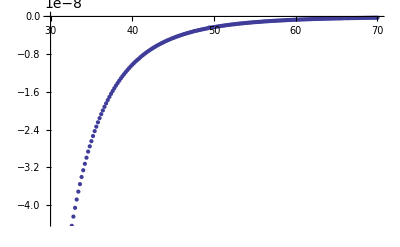

```mathematica
ListPlot[{t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

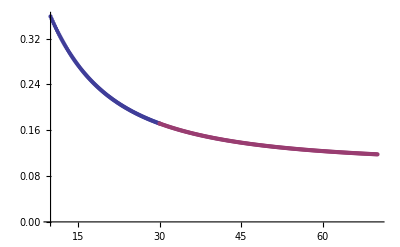

```mathematica
ListPlot[{t1l,t1r,t1r2}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.1/R.dat",Join[t1l,t1r,t1r2]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.1/I.dat",Join[t2r, t2l]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.1/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.990/q=0.1/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```